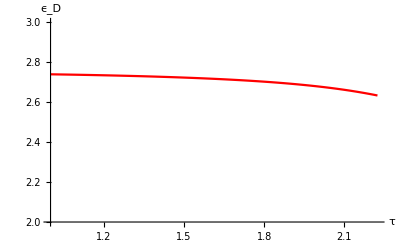

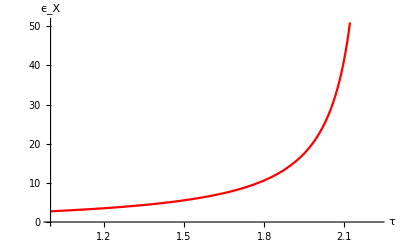

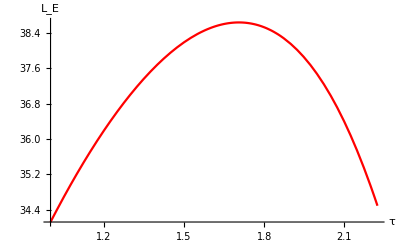

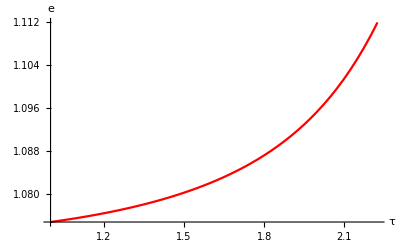

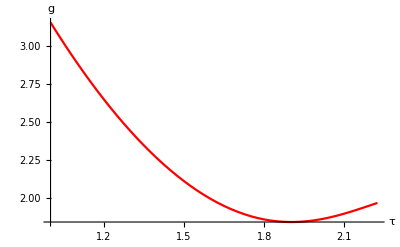

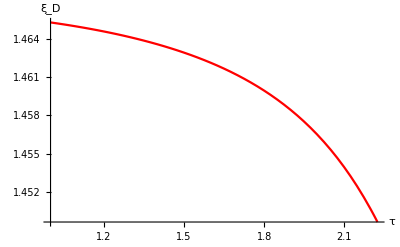

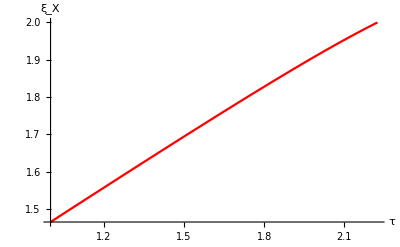

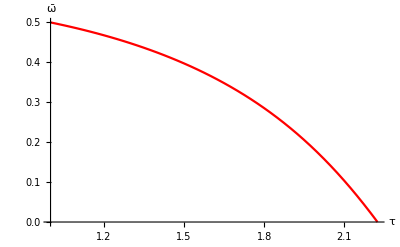

```mathematica
(*This file simulates how the addilog model with Coe-Helpman specification of p_K responds to the change of trade costs.*)
v[x_]=1/(1+γ) (b-x)^(1+γ); 
ϵ[x_]=-(x v''[x])/v'[x];
Subscript[ϵ, D]=ϵ[Subscript[ξ, D]];
Subscript[ϵ, X]=ϵ[Subscript[ξ, X]];
parameters={κ-> 7,ρ->0.8,w->1,L->50,δ->0.25,ψ->1,b->2,γ->1};
eqn1=Subscript[ξ, D] (1-1/Subscript[ϵ, D])τ-Subscript[ξ, X](1-1/Subscript[ϵ, X])==0;
eqn2=1/(ε̃)-(1-ω̃)1/Subscript[ϵ, D]-ω̃ 1/Subscript[ϵ, X]==0;
eqn3=g+δ-(w L)/(κ Subscript[p, K])(1-(v'[Subscript[ξ, D]]+τ v'[Subscript[ξ, X]])/(Subscript[ξ, D] v'[Subscript[ξ, D]]+Subscript[ξ, X] v'[Subscript[ξ, X]]))==0;
eqn4=g-(w L)/(κ Subscript[p, K] ε̃)+(ρ(ε̃-1))/(ε̃)+δ==0;
eqn5= ω̃-(Subscript[ξ, X] v'[Subscript[ξ, X]])/(Subscript[ξ, D] v'[Subscript[ξ, D]]+Subscript[ξ, X] v'[Subscript[ξ, X]])==0;
eqn6= e Subscript[ξ, X](1-1/Subscript[ϵ, X])-τ w==0;
eqn7 =Le (Subscript[ξ, D] v'[Subscript[ξ, D]]+Subscript[ξ, X] v'[Subscript[ξ, X]])-L(v'[Subscript[ξ, D]]+τ v'[Subscript[ξ, X]])==0;
eqn8 = Subscript[p, K]-1/(1+ω̃)==0;

neweqn1L=eqn1/.parameters;
neweqn2L=eqn2/.parameters;
neweqn3L=eqn3/.parameters;
neweqn4L=eqn4/.parameters;
neweqn5L=eqn5/.parameters;
neweqn6L=eqn6/.parameters;
neweqn7L=eqn7/.parameters;
neweqn8L=eqn8/.parameters;
Nvalue=Exp[g] /.parameters;(*we normalize N0=1, and consider t=1 *)
muvalue=Exp[g] (Subscript[ξ, D] v'[Subscript[ξ, D]]+Subscript[ξ, X] v'[Subscript[ξ, X]] );(*we normalize N0=1, and consider t=1 *)
AutEq=v'[Subscript[ξ, X]]==0/.parameters;AutTau=τ/.FindRoot[{AutEq,neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L,neweqn8L},{{τ,2.3},{Subscript[ξ, D],0.5},{Subscript[ξ, X],2},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20},{Subscript[p, K],0.7}}];
additauCH1=Plot[Subscript[ϵ, D]/.parameters/.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L,neweqn8L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20},{ Subscript[p, K],0.7}}],{τ,1,AutTau},PlotRange->{{1,AutTau},{2,3}},PlotStyle-> Red,AxesLabel-> {τ,"ϵ_D" }]
additauCH2=Plot[Subscript[ϵ, X]/.parameters/.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L,neweqn8L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20},{ Subscript[p, K],0.7}}],{τ,1,AutTau},PlotStyle-> Red,AxesLabel-> {τ,"ϵ_X" }]
additauCH3=Plot[Le/.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L,neweqn8L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20},{ Subscript[p, K],0.7}}],{τ,1,AutTau},PlotStyle-> Red,AxesLabel-> {τ,"L_E" }]

additauCH4=Plot[e/.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L,neweqn8L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20},{ Subscript[p, K],0.7}}],{τ,1,AutTau},PlotStyle-> Red,AxesLabel-> {τ,"e" }]
additauCH5=Plot[g/.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L,neweqn8L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20},{ Subscript[p, K],0.7}}],{τ,1,AutTau},PlotStyle-> Red,AxesLabel-> {τ,"g" }]
additauCH6=Plot[Subscript[ξ, D]/.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L,neweqn8L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20},{ Subscript[p, K],0.7}}],{τ,1,AutTau},PlotStyle-> Red,AxesLabel-> {τ,"ξ_D" }]
additauCH7=Plot[Subscript[ξ, X]/.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L,neweqn8L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20},{ Subscript[p, K],0.7}}],{τ,1,AutTau},PlotStyle-> Red,AxesLabel-> {τ,"ξ_X" }]
additauCH8=Plot[ω̃/.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L,neweqn8L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20},{ Subscript[p, K],0.7}}],{τ,1,AutTau},PlotStyle-> Red,AxesLabel-> {τ,"ω̄" }]
additauCH9=Plot[ε̃/.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L,neweqn8L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20},{ Subscript[p, K],0.7}}],{τ,1,AutTau},PlotStyle-> Red,AxesLabel-> {τ,"ϵ̄" }]
additauCH10=Plot[Subscript[ξ, D] e/.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L,neweqn8L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20},{ Subscript[p, K],0.7}}],{τ,1,AutTau},PlotStyle-> Red,AxesLabel-> {τ,"p_D" }]
additauCH11=Plot[Subscript[ξ, X] e/.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L,neweqn8L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20},{ Subscript[p, K],0.7}}],{τ,1,AutTau},PlotStyle-> Red,AxesLabel-> {τ,"p_X" }]
additauCH12=Plot[v'[Subscript[ξ, D]]/muvalue/.parameters /.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L,neweqn8L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20},{ Subscript[p, K],0.7}}],{τ,1,AutTau},PlotStyle-> Red,AxesLabel-> {τ,"x_D"}]
additauCH13=Plot[v'[Subscript[ξ, X]]/muvalue/.parameters /.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L,neweqn8L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20},{ Subscript[p, K],0.7}}],{τ,1,AutTau},PlotStyle-> Red,AxesLabel-> {τ,"x_X"} ]
additauCH14=Plot[κ/(1+ω̃)/.parameters /.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L,neweqn8L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20},{ Subscript[p, K],0.7}}],{τ,1,AutTau},PlotStyle-> Red,AxesLabel-> {τ,"p_Kκ"}]
additauCH15=Plot[1/ρ(Log[v[Subscript[ξ, D]]+v[Subscript[ξ, X]]]+g/ρ)/.parameters /.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L,neweqn8L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20},{ Subscript[p, K],0.7}}],{τ,1,AutTau},AxesOrigin-> {1,0},PlotStyle-> Red,AxesLabel-> {τ,Welfare} ]
```

```mathematica
alladditauCH={{additauCH1,additauCH2,additauCH3,additauCH4},{additauCH5,additauCH6,additauCH7,additauCH8},{additauCH9,additauCH10,additauCH11,additauCH12},{additauCH13,additauCH14,additauCH15}}
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}